

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
FrenetSerretSystem[{Cos[t],Sin[t]},t]
```

{{1},{{-Sin[t],Cos[t]},{-Cos[t],-Sin[t]}}}

```mathematica
Map[Length,{{1},{{-Sin[t],Cos[t]},{-Cos[t],-Sin[t]}}},{1}]
```

{1,2}

```mathematica
FrenetSerretSystem[{1,t,t/4},t,"Cylindrical"]
```

{{16/17,4/17},{{0,4/(√17),1/(√17)},{-1,0,0},{0,-1/(√17),4/(√17)}}}

```mathematica
ParametricPlot3D[CoordinateTransform["Cylindrical"->"Cartesian",{1,t,t/4}]//Evaluate,{t,0, 4Pi},PlotStyle->Thick]
```

-Graphics3D-

```mathematica
CoordinateTransform["Cylindrical"->"Cartesian",{1,t,t/4}]
```

{Cos[t],Sin[t],t/4}

```mathematica
ArcCurvature[{Sin[θ],Cos[θ]},θ]
```

1

```mathematica
ArcCurvature[{x,x},x]
```

0

```mathematica
Simplify[ArcCurvature[{t,t^2},t,"Polar"],t>0]
```

(6 t+8 t^5)/((1+4 t^4)^(3/2))

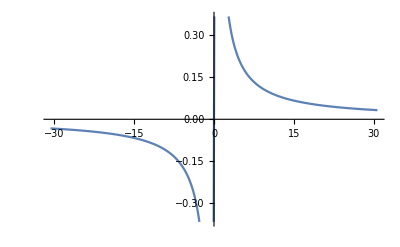

```mathematica
Plot[(6 t+8 t^5)/((1+4 t^4)^(3/2)),{t,-30.68,30.68}]
```

```mathematica
ArcCurvature[{t,t^2},t]
```

2/((1+4 t^2)^(3/2))

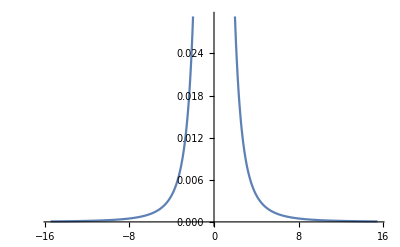

```mathematica
Plot[2/((1+4 t^2)^(3/2)),{t,-15.469999999999999,15.469999999999999}]
```

```mathematica
2ArcCurvature[{t,t^2},t]=={t,f[t]}
```

4/((1+4 t^2)^(3/2))=={t,f[t]}

```mathematica
2ArcCurvature[{t,t^2},t]==f[t]
```

4/((1+4 t^2)^(3/2))==f[t]

```mathematica
Reduce[4/((1+4 t^2)^(3/2))==f[t]]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[4/((1+4 t^2)^(3/2))==f[t]]

```mathematica
ArcCurvature[{t,f[t]},t]
```

√(f''[t]^2/((1+f'[t]^2)^3))

```mathematica
√(f''[t]^2/((1+f'[t]^2)^3))==4/((1+4 t^2)^(3/2))
```

√(f''[t]^2/((1+f'[t]^2)^3))==4/((1+4 t^2)^(3/2))

```mathematica
DSolve[√(f''[t]^2/((1+f'[t]^2)^3))==4/((1+4 t^2)^(3/2)),{f[t],f[t]},{t}]
```

{{f[t]→C[2]+-(√(C[1]^2-C[1]^4+16 K[1]^2+40 C[1]^2 K[1]^2-8 C[1]^4 K[1]^2-192 K[1]^4+144 C[1]^2 K[1]^4-16 C[1]^4 K[1]^4-8 C[1] K[1] √((1+4 K[1]^2)^3)))/(√(1-2 C[1]^2+C[1]^4-24 K[1]^2-48 C[1]^2 K[1]^2+8 C[1]^4 K[1]^2+144 K[1]^4-160 C[1]^2 K[1]^4+16 C[1]^4 K[1]^4))K[1]1t},{f[t]→C[2]+(√(C[1]^2-C[1]^4+16 K[2]^2+40 C[1]^2 K[2]^2-8 C[1]^4 K[2]^2-192 K[2]^4+144 C[1]^2 K[2]^4-16 C[1]^4 K[2]^4-8 C[1] K[2] √((1+4 K[2]^2)^3)))/(√(1-2 C[1]^2+C[1]^4-24 K[2]^2-48 C[1]^2 K[2]^2+8 C[1]^4 K[2]^2+144 K[2]^4-160 C[1]^2 K[2]^4+16 C[1]^4 K[2]^4))K[2]1t},{f[t]→C[2]+-(√(C[1]^2-C[1]^4+16 K[3]^2+40 C[1]^2 K[3]^2-8 C[1]^4 K[3]^2-192 K[3]^4+144 C[1]^2 K[3]^4-16 C[1]^4 K[3]^4+8 C[1] K[3] √((1+4 K[3]^2)^3)))/(√(1-2 C[1]^2+C[1]^4-24 K[3]^2-48 C[1]^2 K[3]^2+8 C[1]^4 K[3]^2+144 K[3]^4-160 C[1]^2 K[3]^4+16 C[1]^4 K[3]^4))K[3]1t},{f[t]→C[2]+(√(C[1]^2-C[1]^4+16 K[4]^2+40 C[1]^2 K[4]^2-8 C[1]^4 K[4]^2-192 K[4]^4+144 C[1]^2 K[4]^4-16 C[1]^4 K[4]^4+8 C[1] K[4] √((1+4 K[4]^2)^3)))/(√(1-2 C[1]^2+C[1]^4-24 K[4]^2-48 C[1]^2 K[4]^2+8 C[1]^4 K[4]^2+144 K[4]^4-160 C[1]^2 K[4]^4+16 C[1]^4 K[4]^4))K[4]1t}}

```mathematica
FullSimplify[√(f''[t]^2/((1+f'[t]^2)^3))==4/((1+4 t^2)^(3/2)),{f'[t],f''[t],t}∈Reals]
```

4 (1+f'[t]^2)^(3/2)==(1+4 t^2)^(3/2) Abs[f''[t]]

```mathematica
DSolve[4 (1+f'[t]^2)^(3/2)==(1+4 t^2)^(3/2) Abs[f''[t]],{f[t],f[t]},{t}]
```

{{f[t]→C[2]+-(√(C[1]^2-C[1]^4+16 K[1]^2+40 C[1]^2 K[1]^2-8 C[1]^4 K[1]^2-192 K[1]^4+144 C[1]^2 K[1]^4-16 C[1]^4 K[1]^4-8 C[1] K[1] √((1+4 K[1]^2)^3)))/(√(1-2 C[1]^2+C[1]^4-24 K[1]^2-48 C[1]^2 K[1]^2+8 C[1]^4 K[1]^2+144 K[1]^4-160 C[1]^2 K[1]^4+16 C[1]^4 K[1]^4))K[1]1t},{f[t]→C[2]+(√(C[1]^2-C[1]^4+16 K[2]^2+40 C[1]^2 K[2]^2-8 C[1]^4 K[2]^2-192 K[2]^4+144 C[1]^2 K[2]^4-16 C[1]^4 K[2]^4-8 C[1] K[2] √((1+4 K[2]^2)^3)))/(√(1-2 C[1]^2+C[1]^4-24 K[2]^2-48 C[1]^2 K[2]^2+8 C[1]^4 K[2]^2+144 K[2]^4-160 C[1]^2 K[2]^4+16 C[1]^4 K[2]^4))K[2]1t},{f[t]→C[2]+-(√(C[1]^2-C[1]^4+16 K[3]^2+40 C[1]^2 K[3]^2-8 C[1]^4 K[3]^2-192 K[3]^4+144 C[1]^2 K[3]^4-16 C[1]^4 K[3]^4+8 C[1] K[3] √((1+4 K[3]^2)^3)))/(√(1-2 C[1]^2+C[1]^4-24 K[3]^2-48 C[1]^2 K[3]^2+8 C[1]^4 K[3]^2+144 K[3]^4-160 C[1]^2 K[3]^4+16 C[1]^4 K[3]^4))K[3]1t},{f[t]→C[2]+(√(C[1]^2-C[1]^4+16 K[4]^2+40 C[1]^2 K[4]^2-8 C[1]^4 K[4]^2-192 K[4]^4+144 C[1]^2 K[4]^4-16 C[1]^4 K[4]^4+8 C[1] K[4] √((1+4 K[4]^2)^3)))/(√(1-2 C[1]^2+C[1]^4-24 K[4]^2-48 C[1]^2 K[4]^2+8 C[1]^4 K[4]^2+144 K[4]^4-160 C[1]^2 K[4]^4+16 C[1]^4 K[4]^4))K[4]1t}}

```mathematica
4 (1+f'[t]^2)^(3/2)==(1+4 t^2)^(3/2) f''[t]
```

4 (1+f'[t]^2)^(3/2)==(1+4 t^2)^(3/2) f''[t]

```mathematica
DSolve[4 (1+f'[t]^2)^(3/2)==(1+4 t^2)^(3/2) f''[t],{f[t],f[t]},{t}]
```

{{f[t]→C[2]+-(√(C[1]^2-C[1]^4+16 K[1]^2+40 C[1]^2 K[1]^2-8 C[1]^4 K[1]^2-192 K[1]^4+144 C[1]^2 K[1]^4-16 C[1]^4 K[1]^4+8 C[1] K[1] √(1+4 K[1]^2)+32 C[1] K[1]^3 √(1+4 K[1]^2)))/(√(1-2 C[1]^2+C[1]^4-24 K[1]^2-48 C[1]^2 K[1]^2+8 C[1]^4 K[1]^2+144 K[1]^4-160 C[1]^2 K[1]^4+16 C[1]^4 K[1]^4))K[1]1t},{f[t]→C[2]+(√(C[1]^2-C[1]^4+16 K[2]^2+40 C[1]^2 K[2]^2-8 C[1]^4 K[2]^2-192 K[2]^4+144 C[1]^2 K[2]^4-16 C[1]^4 K[2]^4+8 C[1] K[2] √(1+4 K[2]^2)+32 C[1] K[2]^3 √(1+4 K[2]^2)))/(√(1-2 C[1]^2+C[1]^4-24 K[2]^2-48 C[1]^2 K[2]^2+8 C[1]^4 K[2]^2+144 K[2]^4-160 C[1]^2 K[2]^4+16 C[1]^4 K[2]^4))K[2]1t}}

```mathematica
HilbertCurve[]
```

HilbertCurve::argt: HilbertCurve called with 0 arguments; 1 or 2 arguments are expected.

HilbertCurve[]

```mathematica
HilbertCurve[1]
```

Line[{{0,0},{0,1},{1,1},{1,0}}]

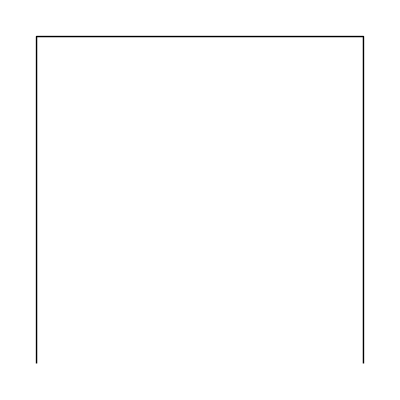

```mathematica
Graphics[HilbertCurve[1]]
```

```mathematica
Manipulate[
Graphics[HilbertCurve[a]]
,{a,1,30,1}]
```

```mathematica
Manipulate[
ArcLength[HilbertCurve[a]]
,{a,1,30,1}]
```

```mathematica
Simplify[ArcCurvature[{t,t^2},t,"Polar"],t>0]
```

(6 t+8 t^5)/((1+4 t^4)^(3/2))

```mathematica
Simplify[ArcCurvature[{-t,t^2},t,"Polar"],t>0]
```

(6 t+8 t^5)/((1+4 t^4)^(3/2))

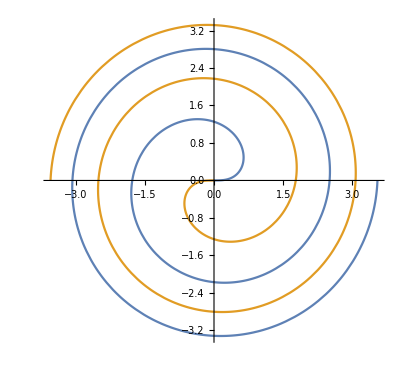

```mathematica
PolarPlot[{Sqrt[t],-Sqrt[t]},{t,0,4Pi}]
```

```mathematica
Show[ParametricPlot3D[Table[{Cos[t]/Cosh[Cot[b]t],Sin[t]/Cosh[Cot[b]t],Tanh[Cot[b]t]}, {b,{Pi/2-.1,Pi/2,Pi/2+.1}}]//Evaluate,{t,0,30}, PlotStyle->Thick,PlotRange->All],Graphics3D[{Opacity[.5],Sphere[]}]]
```

-Graphics3D-

```mathematica
Sin[t]/t
```

Sin[t]/t

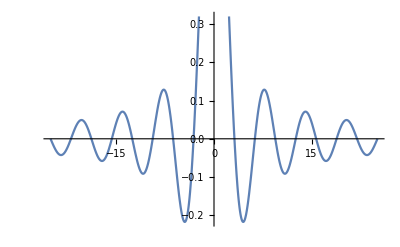

```mathematica
Plot[Sin[t]/t,{t,-25.132741228718345,25.132741228718345}]
```

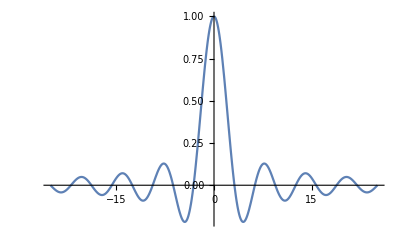

```mathematica
Plot[Sin[t]/t,{t,-25.132741228718345,25.132741228718345},PlotRange->Full]
```

```mathematica
0/0
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
ArcCurvature[a x^2+b x+c,x]
```

2 √(a^2/((1+b^2+4 a b x+4 a^2 x^2)^3))

```mathematica
Manipulate[Plot[2 √(a^2/((1+b^2+4 a b x+4 a^2 x^2)^3)),{x,-8,8}],{a,-8,8},{b,-2,2}]
```

```mathematica
ArcLength[f[x]]
```

ArcLength::reg: f[x] is not a correctly specified region.

ArcLength[f[x]]

```mathematica
ArcLength[{x,f[x]},{x,a,b}]
```

Integrate[√(1+f'[x]^2),{x,a,b},Assumptions→a<b]

```mathematica
1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions->0<a]
```

1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions→0<a]

```mathematica
Solve[1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions->0<a],f'[x]]
```

Solve[1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions→0<a],f'[x]]

```mathematica
1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions->0<a]
```

1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions→0<a]

```mathematica
Solve[1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions->0<a],{a}]
```

Solve[1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions→0<a],{a}]

```mathematica
Reduce[1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions->0<a]]
```

Integrate[√(1+f'[x]^2),{x,0,a},Assumptions→0<a]==1

```mathematica
FindInstance[1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions->0<a],{a,x}]
```

FindInstance::exvar: The system contains a nonconstant expression Assumptions independent of variables {a,x}.

FindInstance[1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions→0<a],{a,x}]

```mathematica
With[{f=Function[x,x^2]},
1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions->0<a]
]
```

1==1/4 (2 a √(1+4 a^2)+ArcSinh[2 a])

```mathematica
Reduce[1==1/4 (2 a √(1+4 a^2)+ArcSinh[2 a])]
```

Reduce[1==1/4 (2 a √(1+4 a^2)+ArcSinh[2 a])]

```mathematica
Reduce[1==1/4 (2 a √(1+4 a^2)+ArcSinh[2 a]),a,]
```

a==Root0.764Root[{-4+Log[2 #1+√(1+4 #1^2)]+2 #1 √(1+4 #1^2)&,0.76392666331709104116}]0.763926663317091

```mathematica
With[{f=Function[x,x^3]},
1==Integrate[√(1+f'[x]^2),{x,0,a},Assumptions->0<a]
]
```

1==a Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]

```mathematica
a Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]
```

a Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]

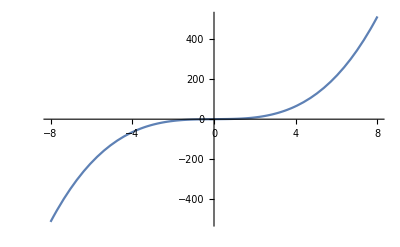

```mathematica
Plot[a Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4],{a,-8,8}]
```

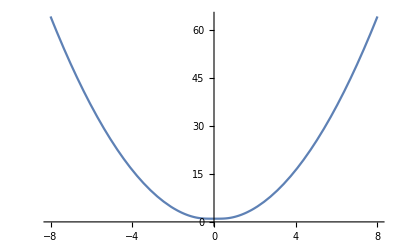

```mathematica
Plot[Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4],{a,-8,8}]
```

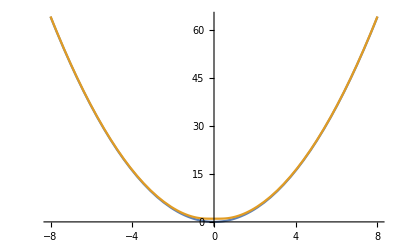

```mathematica
Plot[{a^2,Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]},{a,-8,8}]
```

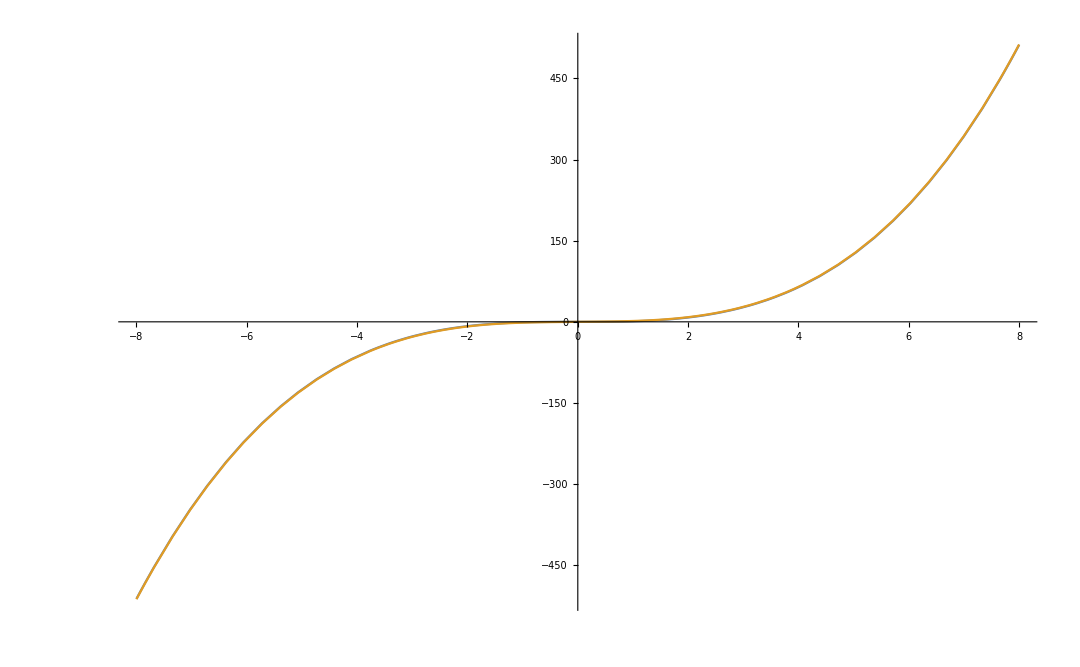

```mathematica
Plot[{a a a,a Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]},{a,-8,8}]
```

```mathematica
Normalize@{a,a Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]}.Normalize@{a,a a a}
```

a^2/(√(Abs[a]^2+Abs[a]^6) √(Abs[a]^2+Abs[a Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]]^2))+(a^4 Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4])/(√(Abs[a]^2+Abs[a]^6) √(Abs[a]^2+Abs[a Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]]^2))

```mathematica
FullSimplify[Normalize@{a,a Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]}.Normalize@{a,a a a},a∈Reals]
```

(a^2+a^4 Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4])/(√((a^4+a^8) (1+Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]^2)))

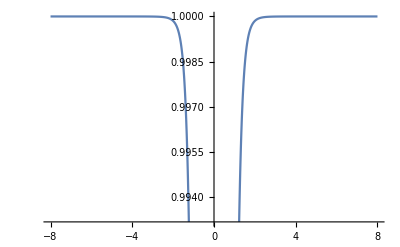

```mathematica
Plot[(a^2+a^4 Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4])/(√((a^4+a^8) (1+Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]^2))),{a,-8,8}]
```

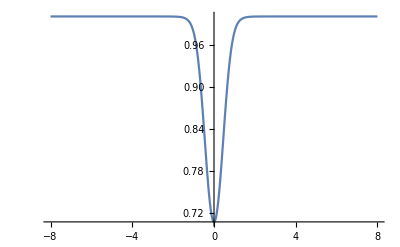

```mathematica
Plot[(a^2+a^4 Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4])/(√((a^4+a^8) (1+Hypergeometric2F1[-1/2,1/4,5/4,-9 a^4]^2))),{a,-8,8},PlotRange->Full]
```

```mathematica
ArcCurvature[{x,x^4},x]
```

(12 Abs[x]^2)/((1+16 x^6)^(3/2))

```mathematica
FullSimplify[ArcCurvature[{x,x^4},x],x∈Reals]
```

(12 x^2)/((1+16 x^6)^(3/2))

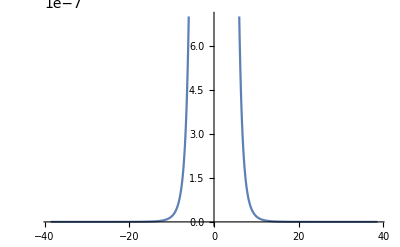

```mathematica
Plot[(12 x^2)/((1+16 x^6)^(3/2)),{x,-38.583999999999996,38.583999999999996}]
```

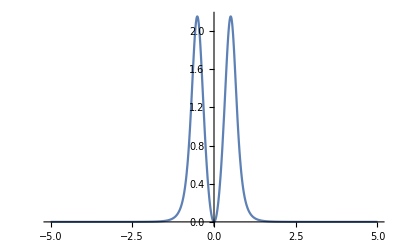

```mathematica
Plot[(12 x^2)/((1+16 x^6)^(3/2)),{x,-5,5},PlotRange->Full]
```

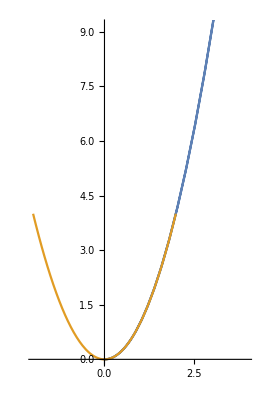

```mathematica
ParametricPlot[{
{x^2,x^4},
{x,x^2}
},{x,-2,2}]
```

```mathematica
f'[x+a]==f'[x]+Integrate[f'[t],{t,x,a}]
```

f'[a+x]==∫_x^a f'[t]ⅆt+f'[x]

```mathematica
f'[x+a]==f'[x]+Integrate[f''[t],{t,x,a}]
```

f'[a+x]==∫_x^a f''[t]ⅆt+f'[x]

```mathematica
f[a+x]==∫_x^a f'[t]ⅆt+f[x]
```

f[a+x]==f[x]+∫_x^a f'[t]ⅆt

```mathematica
Reduce[f[a+x]==f[x]+∫_x^a f'[t]ⅆt]
```

f[x]==f[a+x]-∫_x^a f'[t]ⅆt

```mathematica
f[x]==f[x]-∫_x^a f'[t]ⅆt
```

f[x]==f[x]-∫_x^a f'[t]ⅆt

```mathematica
f[x]==f[x]-∫_x^(x+a) f'[t]ⅆt
```

f[x]==f[x]-∫_x^(a+x) f'[t]ⅆt

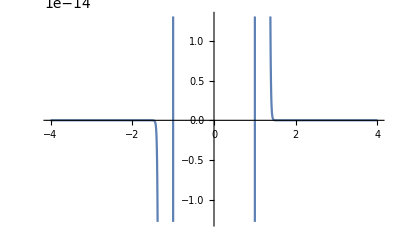

```mathematica
Plot[(x^3-x)/x^100,{x,-4,4}]
```

```mathematica
Plot[(x^3-x)/x^100,{x,-4,4},PlotRange->Full]
```

-Graphics-

```mathematica
{x,√(1-x^2)}
```

{x,√(1-x^2)}

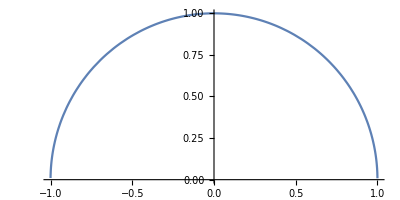

```mathematica
ParametricPlot[
{x,√(1-x^2)}
,{x,-2,2}]
```

```mathematica
Manipulate[
ParametricPlot[
{x,(1-x^y)^(1/y)}
,{x,-2,2}]
,{y,1,10,1}]
```

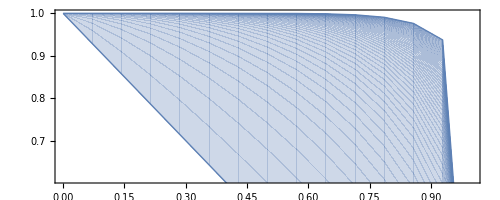

```mathematica
ParametricPlot[
{x,(1-x^y)^(1/y)}
,{x,-2,2},{y,1,10}]
```

```mathematica
ParametricPlot[
{x,(1-x^y)^(1/y)}
,{x,-2,2},{y,1,10}]
```

-Graphics-

```mathematica
Cylinder[]
```

Cylinder[{{0,0,-1},{0,0,1}}]

```mathematica
Graphics3D[Cylinder[]]
```

-Graphics3D-

```mathematica
Volume[Cylinder[]]
```

2 π

```mathematica
a π r^2==2π
```

a π r^2==2 π

```mathematica
Reduce[a π r^2==2 π]
```

r≠0&&a==2/r^2

```mathematica
ArcCurvature[{x,a x^3},x]
```

6 √((a^2 x^2)/((1+9 a^2 x^4)^3))

```mathematica
Manipulate[Plot[6 √((a^2 x^2)/((1+9 a^2 x^4)^3)),{x,-6159.100502872071,6161.421729975723}],{a,-3288.506249534253,3285.4562456171147}]
```

```mathematica
Plot3D[6 √((a^2 x^2)/((1+9 a^2 x^4)^3)),{x,a}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Plot3D[6 √((a^2 x^2)/((1+9 a^2 x^4)^3)),{x,a}∈Disk[{0,0},3],PlotRange->Full]
```

-Graphics3D-

```mathematica
Show[%86,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Plot3D[6 √((a^2 x^2)/((1+9 a^2 x^4)^3)),{x,a}∈Disk[{0,0},3],PlotRange->Full,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
D[6 √((a^2 x^2)/((1+9 a^2 x^4)^3)),a]==0
```

(3 (-(54 a^3 x^6)/((1+9 a^2 x^4)^4)+(2 a x^2)/((1+9 a^2 x^4)^3)))/(√((a^2 x^2)/((1+9 a^2 x^4)^3)))==0

```mathematica
FullSimplify[D[6 √((a^2 x^2)/((1+9 a^2 x^4)^3)),a]==0,{a,x}∈Reals]
```

(a x (-1+18 a^2 x^4))/(√(1+9 a^2 x^4))==0

```mathematica
Reduce[(a x (-1+18 a^2 x^4))/(√(1+9 a^2 x^4))==0]
```

(x≠0&&a==-1/(3 √2 x^2))||(x≠0&&a==1/(3 √2 x^2))||a==0||x==0

```mathematica
Manipulate[
Plot[a x^3,{x,-3,3},PlotRange->{-2,2}]
,{a,-5,5}]
```

```mathematica
Manipulate[
Plot[a (b x)^3,{x,-3,3},PlotRange->{-2,2}]
,{{a,1},-5,5},{{b,1},-5,5}]
```

```mathematica
ll[x,a]==f[a x]/f[a]
```

ll[x,a]==f[a x]/f[a]

```mathematica
With[{f=Function[x,x^3]},
Manipulate[
Plot[f[a x]/f[a],{x,-3,3},PlotRange->{-2,2}]
,{{a,1},-5,5}]
]
```

```mathematica
ArcCurvature[{x,f[x]},x]
```

√(f''[x]^2/((1+f'[x]^2)^3))

```mathematica
ArcCurvature[{x,x^3-x},x]
```

(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2))

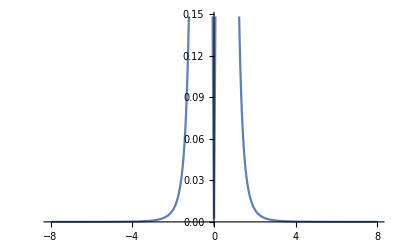

```mathematica
Plot[(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2)),{x,-8,8}]
```

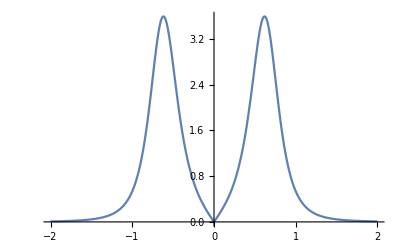

```mathematica
Plot[(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2)),{x,-2,2},PlotRange->Full]
```

```mathematica
ArcCurvature[{x,x x x},x]
```

(6 Abs[x])/((1+9 x^4)^(3/2))

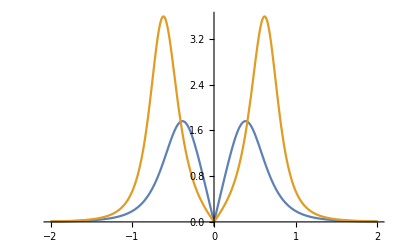

```mathematica
Plot[{(6 Abs[x])/((1+9 x^4)^(3/2)),(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2))},{x,-2,2},PlotRange->Full]
```

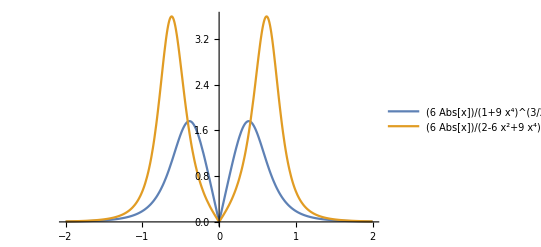

```mathematica
Plot[{(6 Abs[x])/((1+9 x^4)^(3/2)),(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2))},{x,-2,2},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
Area[Circle[]]
```

Undefined

```mathematica
Missing[Undefined]
```

Missing[Undefined]

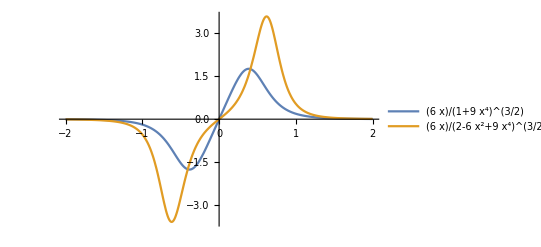

```mathematica
Plot[{(6 x)/((1+9 x^4)^(3/2)),(6 x)/((2-6 x^2+9 x^4)^(3/2))},{x,-2,2},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
Limit[NIntegrate[(6 x)/((2-6 x^2+9 x^4)^(3/2)),{x,0,a}],a->∞]
```

NIntegrate::nlim: x = a is not a valid limit of integration.

lim_(a→∞) NIntegrate[(6 x)/((2-6 x^2+9 x^4)^(3/2)),{x,0,a}]

```mathematica
Manipulate[
NIntegrate[(6 x)/((2-6 x^2+9 x^4)^(3/2)),{x,0,a}],{a,1,10000}]
```

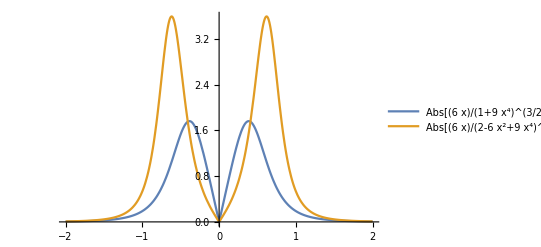

```mathematica
Plot[{Abs[(6 x)/((1+9 x^4)^(3/2))],Abs[(6 x)/((2-6 x^2+9 x^4)^(3/2))]},{x,-2,2},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
and[a,and[b,c]]==and[and[a,b],c]
```

and[a,and[b,c]]==and[and[a,b],c]

```mathematica
FindInstance[and[a,and[b,c]]==and[and[a,b],c],{a,b,c}]
```

FindInstance[and[a,and[b,c]]==and[and[a,b],c],{a,b,c}]

```mathematica
Manipulate[
Plot[
{(6 x)/((1+9 x^4)^(3/2)),(6 (x+a))/((2-6 (x+a)^2+9 (x+a)^4)^(3/2))-(6 (a))/((2-6 (a)^2+9 (a)^4)^(3/2))}
,{x,-2,2}
,PlotRange->Full,PlotLegends->"Expressions"]
,{a,-3,3}]
```

```mathematica
∫_a^b f'[x]ⅆx
```

∫_a^b f'[x]ⅆx

```mathematica
∫_a^b f'[x]ⅆx==f[a]-f[b]
```

∫_a^b f'[x]ⅆx==f[a]-f[b]

```mathematica
ArcCurvature[{t,t}]
```

ArcCurvature::argtu: ArcCurvature called with 1 argument; 2 or 3 arguments are expected.

ArcCurvature[{t,t}]

```mathematica
ArcCurvature[{t,t},t]
```

0

```mathematica
ArcCurvature[{t,t,t},t]
```

0

```mathematica
ArcCurvature[{t,f[t]},t]
```

√(f''[t]^2/((1+f'[t]^2)^3))

```mathematica
ArcCurvature[{t,f[t],g[t]},t]
```

√((f''[t]^2+g'[t]^2 f''[t]^2-2 f'[t] g'[t] f''[t] g''[t]+g''[t]^2+f'[t]^2 g''[t]^2)/((1+f'[t]^2+g'[t]^2)^3))

```mathematica
ArcCurvature[{h[t],f[t],g[t]},t]
```

√((g'[t]^2 f''[t]^2+h'[t]^2 f''[t]^2-2 f'[t] g'[t] f''[t] g''[t]+f'[t]^2 g''[t]^2+h'[t]^2 g''[t]^2-2 f'[t] h'[t] f''[t] h''[t]-2 g'[t] h'[t] g''[t] h''[t]+f'[t]^2 h''[t]^2+g'[t]^2 h''[t]^2)/((f'[t]^2+g'[t]^2+h'[t]^2)^3))

```mathematica
FullSimplify[%119]
```

√((h'[t]^2 (f''[t]^2+g''[t]^2)-2 f'[t] h'[t] f''[t] h''[t]-2 g'[t] g''[t] (f'[t] f''[t]+h'[t] h''[t])+g'[t]^2 (f''[t]^2+h''[t]^2)+f'[t]^2 (g''[t]^2+h''[t]^2))/((f'[t]^2+g'[t]^2+h'[t]^2)^3))

```mathematica
FullSimplify[√((h'[t]^2 (f''[t]^2+g''[t]^2)-2 f'[t] h'[t] f''[t] h''[t]-2 g'[t] g''[t] (f'[t] f''[t]+h'[t] h''[t])+g'[t]^2 (f''[t]^2+h''[t]^2)+f'[t]^2 (g''[t]^2+h''[t]^2))/((f'[t]^2+g'[t]^2+h'[t]^2)^3))
,{t,h[t],h'[t],h''[t],f[t],f'[t],f''[t],g[t],g'[t],g''[t]}∈Reals]
```

√((h'[t]^2 (f''[t]^2+g''[t]^2)-2 f'[t] h'[t] f''[t] h''[t]-2 g'[t] g''[t] (f'[t] f''[t]+h'[t] h''[t])+g'[t]^2 (f''[t]^2+h''[t]^2)+f'[t]^2 (g''[t]^2+h''[t]^2))/((f'[t]^2+g'[t]^2+h'[t]^2)^3))

```mathematica
Solve[√(f''[t]^2/((1+f'[t]^2)^3))==g[t],f'[t]]
```

{{f'[t]→-√(-1+f''[t]^(2/3)/g[t]^(2/3))},{f'[t]→√(-1+f''[t]^(2/3)/g[t]^(2/3))},{f'[t]→-√(-1-f''[t]^(2/3)/(2 g[t]^(2/3))-(ⅈ √3 f''[t]^(2/3))/(2 g[t]^(2/3)))},{f'[t]→√(-1-f''[t]^(2/3)/(2 g[t]^(2/3))-(ⅈ √3 f''[t]^(2/3))/(2 g[t]^(2/3)))},{f'[t]→-√(-1-f''[t]^(2/3)/(2 g[t]^(2/3))+(ⅈ √3 f''[t]^(2/3))/(2 g[t]^(2/3)))},{f'[t]→√(-1-f''[t]^(2/3)/(2 g[t]^(2/3))+(ⅈ √3 f''[t]^(2/3))/(2 g[t]^(2/3)))}}

```mathematica
%122/.Rule->List
```

{{{f'[t],-√(-1+f''[t]^(2/3)/g[t]^(2/3))}},{{f'[t],√(-1+f''[t]^(2/3)/g[t]^(2/3))}},{{f'[t],-√(-1-f''[t]^(2/3)/(2 g[t]^(2/3))-(ⅈ √3 f''[t]^(2/3))/(2 g[t]^(2/3)))}},{{f'[t],√(-1-f''[t]^(2/3)/(2 g[t]^(2/3))-(ⅈ √3 f''[t]^(2/3))/(2 g[t]^(2/3)))}},{{f'[t],-√(-1-f''[t]^(2/3)/(2 g[t]^(2/3))+(ⅈ √3 f''[t]^(2/3))/(2 g[t]^(2/3)))}},{{f'[t],√(-1-f''[t]^(2/3)/(2 g[t]^(2/3))+(ⅈ √3 f''[t]^(2/3))/(2 g[t]^(2/3)))}}}

```mathematica
Solve[√(f''[t]^2/((1+f'[t]^2)^3))==g[t],f'[t],Reals]
```

{{f'[t]→ConditionalExpression[-√Root[g[t]^2+3 g[t]^2 #1+3 g[t]^2 #1^2+g[t]^2 #1^3-f''[t]^2&,1],(f''[t]>√(g[t]^2)&&g[t]>0)||(f''[t]<-√(g[t]^2)&&g[t]>0)]},{f'[t]→ConditionalExpression[√Root[g[t]^2+3 g[t]^2 #1+3 g[t]^2 #1^2+g[t]^2 #1^3-f''[t]^2&,1],(f''[t]>√(g[t]^2)&&g[t]>0)||(f''[t]<-√(g[t]^2)&&g[t]>0)]}}

```mathematica
ArcCurvature[{r Cos[t],r Sin[t]},t]
```

√(1/r^2)

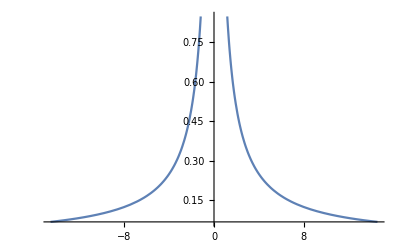

```mathematica
Plot[√(1/r^2),{r,-14.56,14.56}]
```

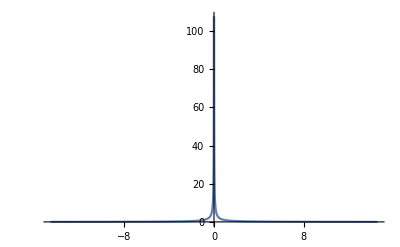

```mathematica
Plot[√(1/r^2),{r,-14.56,14.56},PlotRange->Full]
```

```mathematica
Solve[√(1/r^2)==k,r,Reals]
```

{{r→ConditionalExpression[-1/k,k>0]},{r→ConditionalExpression[1/k,k>0]}}

```mathematica
Solve[√(1/r^2)==k,r,]
```

{{r→ConditionalExpression[1/k,k>0]}}

```mathematica
Solve[√(1/r^2)==k,r,]
```

{{r→ConditionalExpression[1/k,k>0]}}

```mathematica
FrenetSerretSystem[{Cos[t],Sin[t]},t]
```

{{1},{{-Sin[t],Cos[t]},{-Cos[t],-Sin[t]}}}

```mathematica
FrenetSerretSystem[{Cos[t],Sin[t]},t,"Polar"]
```

{{(Cos[t] (Cos[t]^2+Cos[t]^4+3 Sin[t]^2))/((Cos[t]^4+Sin[t]^2)^(3/2))},{{-Sin[t]/(√(Cos[t]^4+Sin[t]^2)),Cos[t]^2/(√(Cos[t]^4+Sin[t]^2))},{-Cos[t]^2/(√(Cos[t]^4+Sin[t]^2)),-Sin[t]/(√(Cos[t]^4+Sin[t]^2))}}}

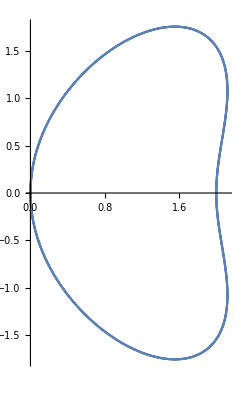

```mathematica
PolarPlot[
{{(Cos[t] (Cos[t]^2+Cos[t]^4+3 Sin[t]^2))/((Cos[t]^4+Sin[t]^2)^(3/2))},{{-Sin[t]/(√(Cos[t]^4+Sin[t]^2)),Cos[t]^2/(√(Cos[t]^4+Sin[t]^2))},{-Cos[t]^2/(√(Cos[t]^4+Sin[t]^2)),-Sin[t]/(√(Cos[t]^4+Sin[t]^2))}}}
,{t,0,2π}]
```

```mathematica
FrenetSerretSystem[{Cos[t],Sin[t],t},t,"Cylindrical"]
```

{{(√((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))/((1+Cos[t]^4+Sin[t]^2)^(3/2)),(Cos[t] (4+5 Cos[t]^2+Cos[t]^4+15 Sin[t]^2))/(1+2 Cos[t]^2+2 Cos[t]^4+2 Cos[t]^6+Cos[t]^8+9 Sin[t]^2+6 Cos[t]^2 Sin[t]^2+6 Cos[t]^4 Sin[t]^2+9 Sin[t]^4)},{{-Sin[t]/(√(1+Cos[t]^4+Sin[t]^2)),Cos[t]^2/(√(1+Cos[t]^4+Sin[t]^2)),1/(√(1+Cos[t]^4+Sin[t]^2))},{-Cos[t]/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))-Cos[t]^3/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))-Cos[t]^5/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))-Cos[t]^7/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))-(3 Cos[t]^3 Sin[t]^2)/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2)),-(3 Cos[t] Sin[t])/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))-(Cos[t]^3 Sin[t])/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))-(Cos[t]^5 Sin[t])/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))-(3 Cos[t] Sin[t]^3)/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2)),-(Cos[t] Sin[t])/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))+(2 Cos[t]^3 Sin[t])/(√(1+Cos[t]^4+Sin[t]^2) √((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))},{(3 Cos[t] Sin[t])/(√((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2)),(-Cos[t]-Cos[t]^3)/(√((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2)),(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)/(√((-Cos[t]-Cos[t]^3)^2+9 Cos[t]^2 Sin[t]^2+(Cos[t]^3+Cos[t]^5+3 Cos[t] Sin[t]^2)^2))}}}

```mathematica
FullSimplify[FrenetSerretSystem[{Cos[t],Sin[t],t},t,"Cylindrical"],t∈Reals]
```

{{(2 Abs[Cos[t]] √(1619-696 Cos[2 t]+108 Cos[4 t]-8 Cos[6 t]+Cos[8 t]))/(15+Cos[4 t])^(3/2),(16 Cos[t] (115-36 Cos[2 t]+Cos[4 t]))/(1619-696 Cos[2 t]+108 Cos[4 t]-8 Cos[6 t]+Cos[8 t])},{{-Sin[t]/(√(1+Cos[t]^4+Sin[t]^2)),Cos[t]^2/(√(1+Cos[t]^4+Sin[t]^2)),1/(√(1+Cos[t]^4+Sin[t]^2))},{-((82+47 Cos[2 t]-2 Cos[4 t]+Cos[6 t]) Sign[Cos[t]])/(√(15+Cos[4 t]) √(1619-696 Cos[2 t]+108 Cos[4 t]-8 Cos[6 t]+Cos[8 t])),-(4 (43-4 Cos[2 t]+Cos[4 t]) Sign[Cos[t]] Sin[t])/(√(15+Cos[4 t]) √(1619-696 Cos[2 t]+108 Cos[4 t]-8 Cos[6 t]+Cos[8 t])),(8 Sec[t] Sign[Cos[t]] Sin[4 t])/(√(15+Cos[4 t]) √(1619-696 Cos[2 t]+108 Cos[4 t]-8 Cos[6 t]+Cos[8 t]))},{(24 √2 Abs[Cos[t]] Tan[t])/(√(1619-696 Cos[2 t]+108 Cos[4 t]-8 Cos[6 t]+Cos[8 t])),-(2 √2 (7 Cos[t]+Cos[3 t]))/(√(Cos[t]^2 (1619-696 Cos[2 t]+108 Cos[4 t]-8 Cos[6 t]+Cos[8 t]))),(8 √2 Abs[Cos[t]] (Cos[t]+Cos[t]^3+3 Sin[t] Tan[t]))/(√(1619-696 Cos[2 t]+108 Cos[4 t]-8 Cos[6 t]+Cos[8 t]))}}}

```mathematica
KnotData["Trefoil"]
```

-Graphics3D-

```mathematica
Volume[KnotData["Trefoil"]]
```

Volume::reg: … is not a correctly specified region.

Volume[-Graphics3D-]